(1 | π/24 | 1-Cos[π/24] | 0.009 | 0.009 | 2 | 9 | 35 | 561 | 561 | 0.0655435 | 4295
2 | π/12 | 1-(1+√3)/(2 √2) | 0.034 | 0.026 | 9 | 35 | 140 | 2233 | 1672 | 0.195509 | 12813
3 | π/8 | 1-Cos[π/8] | 0.076 | 0.042 | 19 | 78 | 312 | 4989 | 2756 | 0.322129 | 21111
4 | π/6 | 1-(√3)/2 | 0.134 | 0.058 | 34 | 137 | 549 | 8780 | 3792 | 0.443238 | 29048
5 | (5 π)/24 | 1-Cos[(5 π)/24] | 0.207 | 0.073 | 53 | 212 | 846 | 13543 | 4763 | 0.556762 | 36488
6 | π/4 | 1-1/(√2) | 0.293 | 0.086 | 75 | 300 | 1200 | 19195 | 5652 | 0.660761 | 43304
7 | (7 π)/24 | 1-Sin[(5 π)/24] | 0.391 | 0.098 | 100 | 401 | 1603 | 25640 | 6445 | 0.753453 | 49378
8 | π/3 | 1/2 | 0.5 | 0.109 | 128 | 512 | 2048 | 32768 | 7128 | 0.833254 | 54608
9 | (3 π)/8 | 1-Sin[π/8] | 0.617 | 0.117 | 158 | 632 | 2529 | 40456 | 7688 | 0.898797 | 58904
10 | (5 π)/12 | 1/4 (4+√2-√6) | 0.741 | 0.124 | 190 | 759 | 3036 | 48574 | 8118 | 0.948962 | 62191
11 | (11 π)/24 | 1-Sin[π/24] | 0.869 | 0.128 | 223 | 890 | 3561 | 56982 | 8408 | 0.98289 | 64415
12 | π/2 | 1 | 1. | 0.131 | 256 | 1024 | 4096 | 65536 | 8554 | 1. | 65536)

(1 | 4295
2 | 12813
3 | 21111
4 | 29048
5 | 36488
6 | 43304
7 | 49378
8 | 54608
9 | 58904
10 | 62191
11 | 64415
12 | 65536
13 | 65536
14 | 64415
15 | 62191
16 | 58904
17 | 54608
18 | 49378
19 | 43304
20 | 36488
21 | 29048
22 | 21111
23 | 12813
24 | 4295
25 | -4295
26 | -12813
27 | -21111
28 | -29048
29 | -36488
30 | -43304
31 | -49378
32 | -54608
33 | -58904
34 | -62191
35 | -64415
36 | -65536
37 | -65536
38 | -64415
39 | -62191
40 | -58904
41 | -54608
42 | -49378
43 | -43304
44 | -36488
45 | -29048
46 | -21111
47 | -12813
48 | -4295)

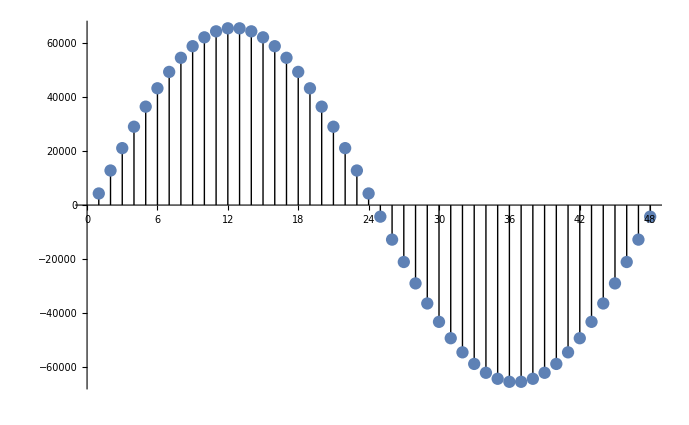

```mathematica
ClearAll;
II3[yy2_]:=Integrate[Sin[x],{x,0,yy2}];
II4[yy2_]:=Integrate[Sin[x],{x,yy2-π/24,yy2}];
II5=Integrate[Sin[x],{x,(11π)/24,(12π)/24}]*(2^16)*1.0;
II9=Table[{
(yy*24)/π, yy,
II3[yy],
Round[1000*II3[yy]]/1000.0,
Round[1000*II4[yy]]/1000.0,
Round[II3[yy]*(2^8)],
Round[II3[yy]*(2^10)],
Round[II3[yy]*(2^12)],
Round[II3[yy]*(2^16)],
Round[II4[yy]*(2^16)],
N[II4[yy]*(2^16)/II5,3],
Round[II4[yy]*(2^16)/II5*(2^16)]

},{yy,1/24 π,π/2,1/24 π}];
II0=Table[{
yy*24/π,
Round[II4[yy]*(2^16)/II5*(2^16)]

},{yy,1/24 π,2π,1/24 π}];
II9//MatrixForm
II0//MatrixForm
ListPlot[II0,Filling->Axis,FillingStyle->Black]
```